```mathematica
Quit[]
```

# Hu-Sawicky Model

### Packages Definitions

```mathematica
<<MaTeX` (* Package to plot with LaTeX format *)
Block[{Print},<<xAct`xPand`]; (* Package to compute cosmological perturbations *)
$DefInfoQ=False; (* No verbose *)
```

```mathematica
DefManifold[M,4,{α,β,γ,η,κ,λ,μ,ν,σ,τ}]
DefMetric[-1,g[-μ,-ν],CD,{";","∇"},PrintAs->"g"]
Block[{Print},SetSlicing[g,n,h,cd,{"|","∂"},"FLFlat"]]; (* Flat FLRW *)
DefMetricFields[g,δg,h];
DefMatterFields[u,δu,h];
MyToxPand[expr_,gauge_,order_]:=ToxPand[expr,δg,u,δu,h, gauge,order]
org[expr_]:=NoScalar@Collect[ContractMetric[expr],$PerturbationParameter,ToCanonical]
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[1,0,0]];
Protect[IndexForm];
PrintAs[ϕh]^="Φ"; (* Gravitational Potentials *)
PrintAs[ψh]^="Ψ";
PrintAs[Eth]^="h"; (* Tensor Modes *)
$ConformalTime=False; (* Cosmic Time *)
$FirstOrderVectorPerturbations=False; (* No Vector Perturbations *)
$FirstOrderTensorPerturbations=False; (* No Tensor Perturbations *)
```

### Notation

One can define a metric different to the default metric in xPand, like the one used in 1904.06294 [astro-ph.CO]:

		 ds^2=-(1+2Ψ)dt^2+a^2(1+2Φ)δ_ij dx^i dx^j

by the following way:

```mathematica
MyGauge={δg[LI[1],-μ_,-ν_]:>-2n[-μ]*n[-ν]*ψh[LI[1]]+2h[-μ,-ν]*ϕh[LI[1]]}
```

{δg | 1 |   |  
  | μ̲ | ν̲:>-2 n^- |  
μ n^- |  
ν Ψ | 1
 +2 h^- |   |  
μ | ν Φ | 1
 }

Then, you can perturb as follows:

```mathematica
PertsExample=ExpandPerturbation@Perturbed[Conformal[g,gah2][g[-μ,-ν]],1];
Pert1stOrder=SplitPerturbations[PertsExample,MyGauge,h]//Expand;
```

```mathematica
VisualizeTensor[Pert1stOrder,h]
```

| n | h
n | -1-2 ϵ (^(1)Ψ^) | 0
h | 0 | (a^)^2 h^- |   |  
μ | ν+2 ϵ (a^)^2 h^- |   |  
μ | ν (^(1)Φ^)

“ToxPand” does not work in this situation, but you can use “ToxPandFromRules”

```mathematica
VisualizeTensor[ToxPandFromRules[g[-μ,-ν],MyGauge,h,1],h]
```

| n | h
n | -1-2 ϵ (^(1)Ψ^) | 0
h | 0 | (a^)^2 h^- |   |  
μ | ν+2 ϵ (a^)^2 h^- |   |  
μ | ν (^(1)Φ^)

```mathematica
(* Notation for derivatives of f(R) *)
DefScalarFunction[FR,PrintAs->"F_R"];
DefScalarFunction[FRR,PrintAs->"F_RR"];

(* 1 order SR parameters for the potentials *)
DefTensor[εΨ[],M,PrintAs->"ε_Ψ"]
DefTensorPerturbation[δεΨ[LI[1]],εΨ[],M,PrintAs->"δε_Ψ"];
DefTensor[εΦ[],M,PrintAs->"ε_Φ"]
DefTensorPerturbation[δεΦ[LI[1]],εΦ[],M,PrintAs->"δε_Φ"];  

(* 2 order SR parameters for the potentials *)
DefTensor[χΨ[],M,PrintAs->"χ_Ψ"]
DefTensorPerturbation[δχΨ[LI[1]],χΨ[],M,PrintAs->"δχ_Ψ"];
DefTensor[χΦ[],M,PrintAs->"χ_Φ"]
DefTensorPerturbation[δχΦ[LI[1]],χΦ[],M,PrintAs->"δχ_Φ"];  

(* SR parameters for the Hubble parameter *)
DefTensor[ε[],M] (* 1 order *)
DefTensorPerturbation[δε[LI[1]],ε[],M,PrintAs->"δε"]; 
 DefTensor[δ[],M] (* 2 order *)
DefTensorPerturbation[δδ[LI[1]],δ[],M,PrintAs->"δδ"];
DefTensor[ξ[],M] (* 3 order *)
DefTensorPerturbation[δξ[LI[1]],ξ[],M,PrintAs->"δξ"]; 
DefTensor[χ[],M] (* 4 order *)
DefTensorPerturbation[δχ[LI[1]],χ[],M,PrintAs->"δχ"];

(* Just to make things more readable *)
(* 1 order perturbation coefficients are red *)
MakeBoxes[εΨ[],StandardForm]:=StyleBox[ToString[εΨ],FontColor->Red]
MakeBoxes[εΦ[],StandardForm]:=StyleBox[ToString[εΦ],FontColor->Red]
(* 2 order perturbation coefficients are blue *)
MakeBoxes[χΨ[],StandardForm]:=StyleBox[ToString[χΨ],FontColor->Blue]
MakeBoxes[χΦ[],StandardForm]:=StyleBox[ToString[χΦ],FontColor->Blue]

(* Background SR parameters *)
MakeBoxes[ε[],StandardForm]:=StyleBox[ToString[ε],FontColor->Orange]
MakeBoxes[δ[],StandardForm]:=StyleBox[ToString[δ],FontColor->Purple]
MakeBoxes[ξ[],StandardForm]:=StyleBox[ToString[ξ],FontColor->Pink]
MakeBoxes[χ[],StandardForm]:=StyleBox[ToString[χ],FontColor->Brown]

(* Matter sector *)
DefScalarFunction[ρm,PrintAs->"ρ_m"];
DefScalarFunction[δm,PrintAs->"δ_m"];
DefScalarFunction[Vm,PrintAs->"V_m"];
```

## Background

```mathematica
DefScalarFunction[HN,PrintAs->"H"];
DefScalarFunction[aN,PrintAs->"a"];
```

```mathematica
ρDE=-f/2+3 (H^)^2+3 F (H^)^2+3 F Ḣ-3 H^ F'; (* DE density *)
PDE=f/2-3 (H^)^2-3 F (H^)^2-2 Ḣ-F Ḣ+2 H^ F'+F'';(* DE pressure *)
```

```mathematica
(* In ⅇ-folds time -> dt = a*dη = dN/H ⇒ dN = (a*H)dη *)
ρDENe=ρDE/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.f->f[R]/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FR->f''[R]//Expand
PDENe=PDE/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.f->f[R]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]//Expand
```

-f[R]/2+3 H[Ne]^2+3 H[Ne]^2 f'[R]+3 H[Ne] f'[R] H'[Ne]-3 H[Ne]^2 Ra'[Ne] f''[R]

f[R]/2-3 H[Ne]^2-3 H[Ne]^2 f'[R]-2 H[Ne] H'[Ne]-H[Ne] f'[R] H'[Ne]+2 H[Ne]^2 Ra'[Ne] f''[R]+H[Ne] H'[Ne] Ra'[Ne] f''[R]+H[Ne]^2 f''[R] Ra''[Ne]+H[Ne]^2 Ra'[Ne]^2 f^(3)[R]

```mathematica
(* Approximated expression for H -> See eq. in Savvas' f(R)_numerics_HS.nb *)
Happ[Ne_]:=H0 Sqrt[1-om+om/a^3-Ωr+Ωr/a^4+(2 a^2 b (-1+om+Ωr)^2 (-6 a om^2-7 om Ωr+3 a^4 om (-1+om+Ωr)+4 a^3 Ωr (-1+om+Ωr)+12 a^7 (-1+om+Ωr)^2))/(-om+4 a^3 (-1+om+Ωr))^3-(a^5 b^2 (-1+om+Ωr)^3 (-37 a om^6-40 om^5 Ωr+4656 a^4 om^5 (-1+om+Ωr)+8692 a^3 om^4 Ωr (-1+om+Ωr)+4032 a^2 om^3 Ωr^2 (-1+om+Ωr)+7452 a^7 om^4 (-1+om+Ωr)^2+25728 a^6 om^3 Ωr (-1+om+Ωr)^2+17856 a^5 om^2 Ωr^2 (-1+om+Ωr)^2-25408 a^10 om^3 (-1+om+Ωr)^3-22016 a^9 om^2 Ωr (-1+om+Ωr)^3+9216 a^8 om Ωr^2 (-1+om+Ωr)^3+22848 a^13 om^2 (-1+om+Ωr)^4+2048 a^12 om Ωr (-1+om+Ωr)^4-9216 a^16 om (-1+om+Ωr)^5-3072 a^15 Ωr (-1+om+Ωr)^5-1024 a^19 (-1+om+Ωr)^6))/(om-4 a^3 (-1+om+Ωr))^8]/.Ωr->0/.om->Ωm0/.+1-Ωm0->ΩΛ/.-1+Ωm0->-ΩΛ/.a->Exp[Ne]//Simplify
```

```mathematica
Happ[Log[a]]
Happ[Log[a]]/.ΩΛ->0//FullSimplify
```

H0 √(Ωm0/a^3+ΩΛ-(6 a^3 b ΩΛ^2 (-2 Ωm0^2-a^3 Ωm0 ΩΛ+4 a^6 ΩΛ^2))/((Ωm0+4 a^3 ΩΛ)^3)+(a^5 b^2 ΩΛ^3 (-37 a Ωm0^6-4656 a^4 Ωm0^5 ΩΛ+7452 a^7 Ωm0^4 ΩΛ^2+25408 a^10 Ωm0^3 ΩΛ^3+22848 a^13 Ωm0^2 ΩΛ^4+9216 a^16 Ωm0 ΩΛ^5-1024 a^19 ΩΛ^6))/((Ωm0+4 a^3 ΩΛ)^8))

H0 √(Ωm0/a^3)

```mathematica
aN[Ne_]:=Exp[Ne] (* Scale factor in terms of N *)
Ωm[Ne_]:=Ωm0 aN[Ne]^-3 (* Matter density parameter *)
HN[Ne_]:=Happ[Ne] (* Hubble parameter in N time *)
Ra[Ne_]:=6(2 HN[Ne]^2+HN[Ne]*HN'[Ne]) (* Ricci scalar *)
(* Hu-Sawicky -> See Eq. (56) in 1811.02469 *)
f[R_]:=R-(2Λ)/(1+b*Λ/R)/.Λ->3*H0^2 ΩΛ;
ρDEHS[a_]:=ρDENe/.R->Ra[Ne]/.Ne->Log[a]//Simplify (* DE Density *)
```

```mathematica
(* Equation of state of DE *)
wHS[a_]:=PDENe/ρDENe/.R->Ra[Ne]/.Ne->Log[a]
Series[wHS[a],{a,0,5}]//Simplify
Series[wHS[a],{b,0,1}]/.ΩΛ->1-Ωm0//Simplify (* This is Eq. (59) in 1811.02469 *)
```

-1-(12 (b ΩΛ) a^3)/Ωm0+O[a]^6

-1-(12 (a^3 (-1+Ωm0) Ωm0 (8 a^6 (-1+Ωm0)^2-7 a^3 (-1+Ωm0) Ωm0-Ωm0^2)) b)/((-4 a^3 (-1+Ωm0)+Ωm0)^4)+O[b]^2

```mathematica
(* Directly from formula *)
STwHS[a_]:=-(f-6 (1+F) (H^)^2-2 (2+F) Ḣ+4 H^ F'+2 F'')/(f-6 (1+F) (H^)^2-6 F Ḣ+6 H^ F')/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.f->f[R]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a]
Series[STwHS[a],{a,0,3}]//Simplify
Series[STwHS[a],{b,0,1}]/.ΩΛ->1-Ωm0//Simplify (* This is Eq. (59) in 1811.02469 *)
```

-1-(12 (b ΩΛ) a^3)/Ωm0+O[a]^4

-1-(12 (a^3 (-1+Ωm0) Ωm0 (8 a^6 (-1+Ωm0)^2-7 a^3 (-1+Ωm0) Ωm0-Ωm0^2)) b)/((-4 a^3 (-1+Ωm0)+Ωm0)^4)+O[b]^2

```mathematica
H0=1; (* Hubble parameter today *);
h=0.67810; (* Reduced Hubble parameter *)
ωb=0.02238280; (* Subscript[Ω, b] h^2 *)
ωCDM=0.1201075; (* Subscript[Ω, CDM] h^2 *)
ωm=ωCDM+ωb;
Ωm0=(ωb+ωCDM)/h^2; (* Matter Today *)
ΩΛ=1-Ωm0; (* Dark Energy Today *)
fR0[b_]:=f'[R]-1/.R->Ra[Ne]/.Ne->Log[1] 
Solve[fR0[b]==-10^-4,b]//Quiet (* Value of b from Subscript[f, R,0] = -10^-4 -> See comment after Eq. (70) in 1811.02469 *)
bHS=%[[3,1,2]]
```

{{b→-191.353-352.747 ⅈ},{b→-191.353+352.747 ⅈ},{b→0.000989557},{b→418.617}}

0.000989557

```mathematica
0.0009895571321376874
```

0.000989557

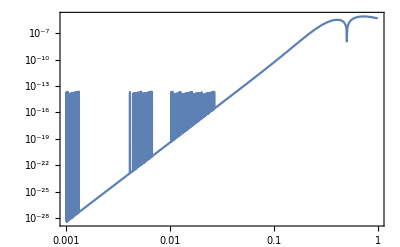

```mathematica
(* Approximation at first order in b *)
LogLogPlot[{Abs[(Happ[Log[a]]^2-(Ωm+ΩΛ+(6 b ΩΛ^2 (2 Ωm^2+Ωm ΩΛ-4 ΩΛ^2))/(Ωm+4 ΩΛ)^3))/Happ[Log[a]]^2]*100}/.Ωm->Ωm0*a^-3/.b->bHS//Abs,{a,10^-3,1},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13}]
```

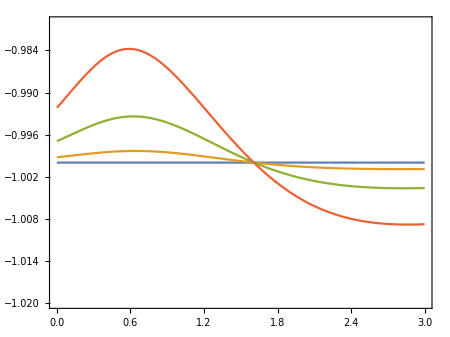

```mathematica
(* This is Fig. 1 in 1811.02469 *)
PlotwHS=Plot[wHS[a]/.b->{0,0.005,0.02,0.05}/.a->(1+z)^-1//Evaluate,{z,0,3},PlotRange->{-1+{-1,1}/50},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"z","w_\\text{DE}"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.75,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["b = 0"],
(MaTeX[#,Magnification->1.2]&)/@Style["b = 0.0005"],
(MaTeX[#,Magnification->1.2]&)/@Style["b = 0.0020"],
(MaTeX[#,Magnification->1.2]&)/@Style["b = 0.0050"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->None],
{0.16,0.24}],Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.92,0.92}]]},ImageSize->450]
```

```mathematica
wHSapprox[a_]:=Normal[Series[wHS[a],{b,0,1}]/.ΩΛ->1-Ωm0]
```

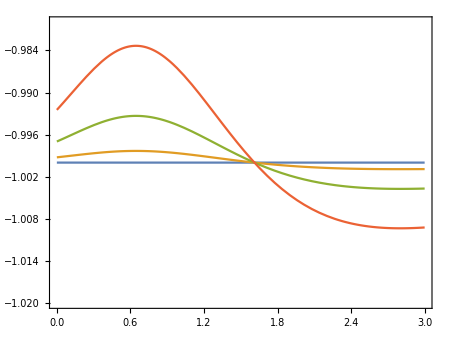

```mathematica
(* The approximation is really good at low redshift *)
PlotwHS=Plot[wHSapprox[a]/.b->{0,0.005,0.02,0.05}/.a->(1+z)^-1//Evaluate,{z,0,3},PlotRange->{-1+{-1,1}/50},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"z","w_\\text{DE}"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.75,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["b = 0"],
(MaTeX[#,Magnification->1.2]&)/@Style["b = 0.0005"],
(MaTeX[#,Magnification->1.2]&)/@Style["b = 0.0020"],
(MaTeX[#,Magnification->1.2]&)/@Style["b = 0.0050"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->None],
{0.16,0.24}],Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.92,0.92}]]},ImageSize->450]
```

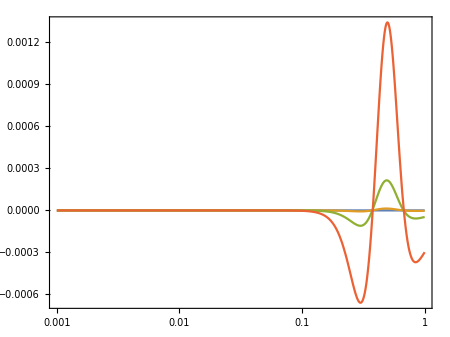

```mathematica
(* The approximation is really good! Some differences at low-z and large b *)
LogLinearPlot[{wHSapprox[a]-wHS[a]}/.b->{0,0.005,0.02,0.05}//Evaluate,{a,0.001,1},PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"z","w_\\text{DE}"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.75,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["b = 0"],
(MaTeX[#,Magnification->1.2]&)/@Style["b = 0.0005"],
(MaTeX[#,Magnification->1.2]&)/@Style["b = 0.0020"],
(MaTeX[#,Magnification->1.2]&)/@Style["b = 0.0050"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->None],
{0.16,0.24}],Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.92,0.92}]]},ImageSize->450]
```

## Sub-Horizon Parameters

```mathematica
εSHA[Ne_,k_]:=(ⅇ^Ne*HN[Ne])/k
```

```mathematica
(* In general δ is non-negligible*)
δSHA[Ne_,k_]:=D[εSHA[Nⅇ,k],Nⅇ]/εSHA[Nⅇ,k]/.Nⅇ->Ne//Simplify
```

```mathematica
δSHA[Ne,k]/.b->bHS/.k->0/.Ne->Log[a]/.a->{0.01,0.1,1}
```

{-0.499997,-0.496667,0.534953}

```mathematica
(* In general -> ξ = 1 is non-negligible*)
ξSHA[Ne_,k_]:=D[HN[Nⅇ]*D[εSHA[Nⅇ,k],Nⅇ],Nⅇ]/(HN[Nⅇ]*εSHA[Nⅇ,k])/.Nⅇ->Ne//Simplify
```

```mathematica
ξSHA[Ne,k]/.b->bHS/.k->0/.Ne->Log[a]/.a->{0.01,0.1,1}
```

{1.,1.,0.999929}

```mathematica
(* In general χ is non-negligible*)
χSHA[Ne_,k_]:=(HN[Nⅇ]*D[HN[Nⅇ]*D[HN[Nⅇ]*D[εSHA[Nⅇ,k],Nⅇ],Nⅇ],Nⅇ])/(HN[Nⅇ]^3*εSHA[Nⅇ,k])/.Nⅇ->Ne//Simplify
```

```mathematica
χSHA[Ne,k]/.b->bHS/.k->100/.Ne->Log[a]/.a->{0.01,0.1,1}//Quiet
```

{-3.49999,-3.49,-0.394704}

```mathematica
(* Usually ε enter in even powers -> ε^2 < 10^-3 for k > 180 H0 *)Manipulate[LogLogPlot[{εSHA[Log[a],k]^2/.b->bHS,1,0.1,0.01,0.001}//Evaluate,{a,10^-2,1},PlotRange->All,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->12}],{k,1,600,20},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a","\\varepsilon^2"},RotateLabel->False]
```

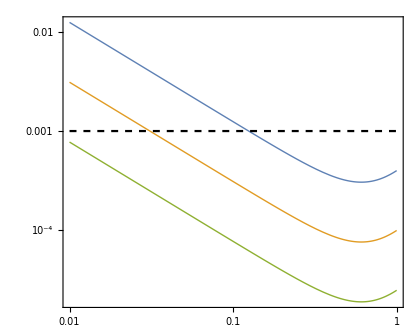

```mathematica
(* This is Fig.  in 2303. -> Hardly any difference with ΛCDM *)
LogLogPlot[{εSHA[Log[a],50H0]^2,εSHA[Log[a],100H0]^2,εSHA[Log[a],200H0]^2,0.001}/.b->bHS//Evaluate,{a,10^-2,1},PlotRange->{All,{0.1,10^-5}},PlotStyle->{Directive[Thick],Directive[Thick],Directive[Thick],Directive[Dashed,Black]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"a","\\varepsilon^2"},RotateLabel->False,BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.8,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["k = 50 H_0"],
(MaTeX[#,Magnification->1.2]&)/@Style["k = 100 H_0"],
(MaTeX[#,Magnification->1.2]&)/@Style["k = 200 H_0"]},
LegendLayout->{"Row",3},LegendMarkerSize->{35,15},LabelStyle->{Black,Bold,15},LegendFunction->Frame],
{0.8,0.78}],ImageSize->420]
```

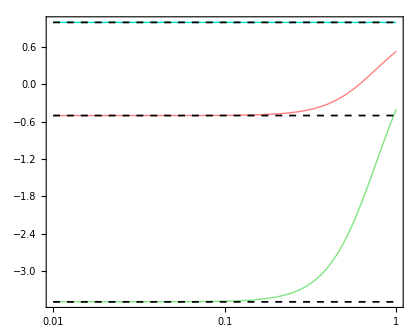

```mathematica
(* This is Fig.  in 2303. *)
LogLinearPlot[{δSHA[Log[a],k],ξSHA[Log[a],k],χSHA[Log[a],k],-0.5,-3.5,1}/.b->bHS//Evaluate,{a,10^-2,1},PlotRange->All,PlotStyle->{Directive[Thick,RGBColor[1,0.5,0.5]],Directive[Thick,RGBColor[0.,0.9,0.8]],Directive[Thick,RGBColor[0.5,0.9,0.5]],Directive[Dashed,Black,Thickness[0.003]],Directive[Dashed,Black,Thickness[0.003]],Directive[Dashed,Black,Thickness[0.003]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->0.8,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\delta"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\xi"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\chi"]},
LegendLayout->{"Row",3},LegendMarkerSize->{40,5},LabelStyle->{Black,Bold,15},LegendFunction->Frame],
{0.2,0.38}],ImageSize->420]//Quiet
```

## Perturbations

### Standard QSA and SHA

#### Expressions

```mathematica
Φstd[Ne_]:=(2 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
Ψstd[Ne_]:=-(4 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δρDEstd[Ne_]:=-((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)/(F (3 Subscript[F, R] k^2+F (a^)^2))/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δPDEstd[Ne_]:=(2 Subscript[F, R] k^4+15 Subscript[F, R] k^2 (a^)^2 F''+3 F (a^)^4 F'')/(9 F Subscript[F, R] k^4+3 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]/.R->Ra[Ne]
VDEstd[Ne_]:=(a^ (6 Subscript[F, R] k^2+F (a^)^2) F')/(2 F (3 Subscript[F, R] k^2+F (a^)^2))/.ah[]->aN[Ne]/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]
πDEstd[Ne_]:=1/F*(k^2/a^2*FR/F)/(1+3 k^2/a^2*FR/F)/.a->aN[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);
Φistd=Φstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.b->bHS/.k->300H0/.a->ai//Quiet;
Ψistd=Ψstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.b->bHS/.k->300H0/.a->ai//Quiet;

(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[Φstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a];
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])Ψstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsstd=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.b->bHS/.k->300H0,{δm,Vm},{a,ai,1},MaxStepSize->10^-4,MaxStepFraction->10^-4,StartingStepSize->10^-4,PrecisionGoal->11,AccuracyGoal->11,MaxSteps->20000000,InterpolationOrder->All,Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### Results

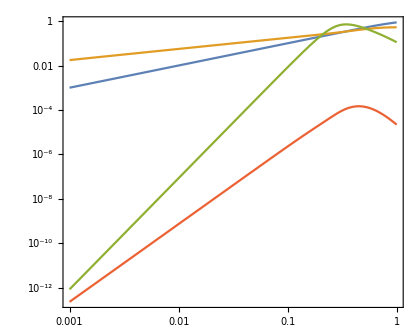

```mathematica
LogLogPlot[{δm[a],Vm[a],δρDEstd[Log[a]]*(3 H0^2 Ωm[Log[a]])/ρDEHS[a] δm[a],VDEstd[Log[a]]*(3 H0^2 Ωm[Log[a]])/ρDEHS[a] δm[a]}/.b->bHS/.k->300H0/.SolPertsstd//Abs//Evaluate,{a,ai,1},PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.8,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_m"],
(MaTeX[#,Magnification->1.3]&)/@Style["V_m"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}"],
(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.885,0.23}],ImageSize->420]//Quiet
```

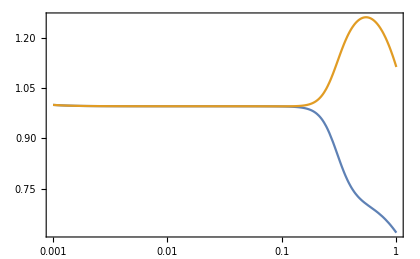

```mathematica
LogLinearPlot[{(Φstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Φstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai]),(Ψstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Ψstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])}/.b->bHS/.k->300H0/.SolPertsstd//Evaluate,{a,ai,1},Frame->True,PlotRange->All,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},PlotLegends->(MaTeX[#,Magnification->1.4]&)/@{"\\Phi/\\Phi_i","\\Psi/\\Psi_i"},BaseStyle->{FontFamily->"Times",FontSize->13},ImageSize->420]
```

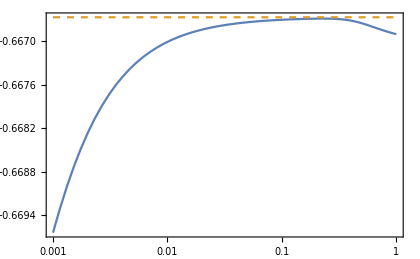

```mathematica
LogLinearPlot[{δPDEstd[Log[a]]/δρDEstd[Log[a]],-2/3}/.b->bHS/.k->300H0/.SolPertsstd//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{"",Directive[Dashed]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"a","c_s^2"},BaseStyle->{FontFamily->"Times",FontSize->13},RotateLabel->False,ImageSize->420]
```

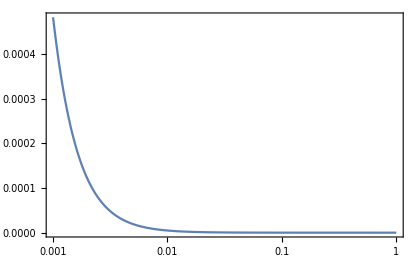

```mathematica
LogLinearPlot[{δPDEstd[Log[a]]/δρDEstd[Log[a]]-2/3*πDEstd[Log[a]]/δρDEstd[Log[a]]}/.b->bHS/.k->300H0//Evaluate,{a,ai,1},PlotRange->Full,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"a","c_\\text{eff}^2"},BaseStyle->{FontFamily->"Times",FontSize->13},RotateLabel->False,ImageSize->420]
```

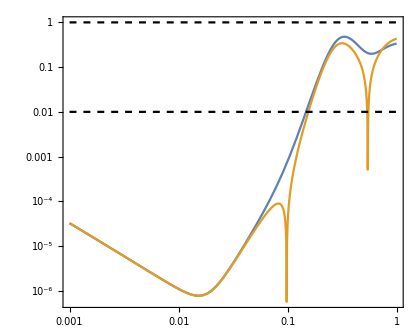

```mathematica
(* Check the consistency of QSA *)
LogLogPlot[{D[Φstd[Log[A]]*3 H0^2 Ωm[Log[A]]*δm[A],A]/(Φstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]a*HN[Log[a]]^2),D[Ψstd[Log[A]]*3 H0^2 Ωm[Log[A]]*δm[A],A]/(Ψstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2),0.01,1}/.A->a/.b->bHS/.k->300H0/.SolPertsstd//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{"","",Directive[Black,Dashed],Directive[Black,Dashed]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.8,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["|\\varepsilon_\\Phi|"],
(MaTeX[#,Magnification->1.3]&)/@Style["|\\varepsilon_\\Psi|"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,15},LegendFunction->Frame],
{0.85,0.2}],ImageSize->420]
```

### 0^th Order in QSA

#### 0^th Order in SHA

```mathematica
(* Don't forget the factors Subscript[ρ̄, m] Subscript[δ, m] for the potentials and Subscript[ρ̄, m]/Subscript[ρ̄, DE] Subscript[δ, m] for the other perturbations *)
ΦQSASHA0[Ne_]:=(2 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
ΨQSASHA0[Ne_]:=-(4 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
δρQSASHA0[Ne_]:=((2-3 F) Subscript[F, R] k^2-(-1+F) F (a^)^2)/(F (3 Subscript[F, R] k^2+F (a^)^2))/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
δPQSASHA0[Ne_]:=(2 Subscript[F, R] k^2)/(9 F Subscript[F, R] k^2+3 F^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
VQSASHA0[Ne_]:=0
cs2QSASHA0[Ne_]:=-(2 (Subscript[F, R] k^2))/(3 (-2+3 F) Subscript[F, R] k^2+3 (-1+F) F (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor [z = 68] *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);

(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[ΦQSASHA0[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a];
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])ΨQSASHA0[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsQSASHA0=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.b->bHS/.k->300H0,{δm,Vm},{a,ai,1},Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### 2^nd Order in SHA

```mathematica
(* Don't forget the factors Subscript[ρ̄, m] Subscript[δ, m] for the potentials and Subscript[ρ̄, m]/Subscript[ρ̄, DE] Subscript[δ, m] for the other perturbations *)
ΦQSASHA2[Ne_]:=(2 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)-(3 ((a^)^2 (F^2 (a^)^4+F Subscript[F, R] k^2 (a^)^2 (8+δ)+2 Subscript[F, R]^2 k^4 (8+3 δ))) ε^2)/(2 (F (3 Subscript[F, R] k^3+F k (a^)^2)^2))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
ΨQSASHA2[Ne_]:=-(4 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)+(3 (a^)^2 (4 Subscript[F, R] k^2+F (a^)^2) (F (a^)^2+Subscript[F, R] k^2 (2-3 δ)) ε^2)/(2 F (3 Subscript[F, R] k^3+F k (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
δρQSASHA2[Ne_]:=((2-3 F) Subscript[F, R] k^2-(-1+F) F (a^)^2)/(F (3 Subscript[F, R] k^2+F (a^)^2))-(3 (Subscript[F, R] k^2 (F (a^)^2 (1+δ)+2 Subscript[F, R] k^2 (2+3 δ))) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
δPQSASHA2[Ne_]:=(2 Subscript[F, R] k^2)/(9 F Subscript[F, R] k^2+3 F^2 (a^)^2)+(((-1+F) F^2 (a^)^4 (1+2 δ)+F Subscript[F, R] k^2 (a^)^2 (-5+5 F-10 δ+13 F δ)+Subscript[F, R]^2 k^4 (-4-6 δ+3 F (2+7 δ))) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
VQSASHA2[Ne_]:=(((-4+3 F) Subscript[F, R] k^3+(-1+F) F k (a^)^2) ε)/(F (3 Subscript[F, R] k^2+F (a^)^2))/.ε->εSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
πQSASHA2[Ne_]:=(Subscript[F, R] k^2)/(3 F Subscript[F, R] k^2+F^2 (a^)^2)+(3 Subscript[F, R] k^2 (Subscript[F, R] k^2 (4+9 δ)+(a^)^2 (F+2 F δ)) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
cs2QSASHA2[Ne_]:=-(2 (Subscript[F, R] k^2))/(3 (-2+3 F) Subscript[F, R] k^2+3 (-1+F) F (a^)^2)-(F ((-1+F)^2 F (a^)^4 (1+2 δ)+Subscript[F, R]^2 k^4 (-8+6 F-20 δ+21 F δ)+(-1+F) Subscript[F, R] k^2 (a^)^2 (-4-8 δ+F (5+13 δ))) ε^2)/(((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
cs2effQSASHA2[Ne_]:=((-((-1+F) F (a^)^2 (1+2 δ))+Subscript[F, R] k^2 (4+8 δ-F (2+7 δ))) ε^2)/((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);
ΦiQSASHA=ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.b->bHS/.k->300/.a->ai//Quiet;
ΨiQSASHA=ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.b->bHS/.k->300/.a->ai//Quiet;

(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a];
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsQSASHA2=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.b->bHS/.k->300H0,{δm,Vm},{a,ai,1},Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### 4^th Order in SHA

```mathematica
(* Don't forget the factors Subscript[ρ̄, m] Subscript[δ, m] for the potentials and Subscript[ρ̄, m]/Subscript[ρ̄, DE] Subscript[δ, m] for the other perturbations *)
ΦQSASHA4[Ne_]:=(2 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)-(3 ((a^)^2 (F^2 (a^)^4+F Subscript[F, R] k^2 (a^)^2 (8+δ)+2 Subscript[F, R]^2 k^4 (8+3 δ))) ε^2)/(2 (F (3 Subscript[F, R] k^3+F k (a^)^2)^2))-1/(2 (F^2 k^2 (3 Subscript[F, R] k^2+F (a^)^2)^3))9 (-F^4 (a^)^8-2 F^3 Subscript[F, R] k^2 (a^)^6 (7-δ+δ^2-ξ)+60 Subscript[F, R]^4 k^8 (-2+δ+ξ)+F^2 Subscript[F, R]^2 k^4 (a^)^4 (-72+26 δ-7 δ^2+20 ξ)+2 F Subscript[F, R]^3 k^6 (a^)^2 (-78+43 δ+3 δ^2+31 ξ)) ε^4/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
ΨQSASHA4[Ne_]:=-(4 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)+(3 (a^)^2 (4 Subscript[F, R] k^2+F (a^)^2) (F (a^)^2+Subscript[F, R] k^2 (2-3 δ)) ε^2)/(2 F (3 Subscript[F, R] k^3+F k (a^)^2)^2)+(9 (4 Subscript[F, R] k^2+F (a^)^2) (-F^3 (a^)^6+30 Subscript[F, R]^3 k^6 (-2+δ+ξ)+2 F^2 Subscript[F, R] k^2 (a^)^4 (-4+3 δ-δ^2+ξ)+F Subscript[F, R]^2 k^4 (a^)^2 (-36+22 δ-15 δ^2+16 ξ)) ε^4)/(2 F^2 k^2 (3 Subscript[F, R] k^2+F (a^)^2)^3)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
δρQSASHA4[Ne_]:=((2-3 F) Subscript[F, R] k^2-(-1+F) F (a^)^2)/(F (3 Subscript[F, R] k^2+F (a^)^2))-(3 (Subscript[F, R] k^2 (F (a^)^2 (1+δ)+2 Subscript[F, R] k^2 (2+3 δ))) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)+(9 Subscript[F, R] k^2 (F^2 Subscript[F, R] k^2 (a^)^4 (46-5 δ+7 δ^2-20 ξ)+F^3 (a^)^6 (5+δ+2 δ^2-2 ξ)-60 Subscript[F, R]^3 k^6 (-2+δ+ξ)-2 F Subscript[F, R]^2 k^4 (a^)^2 (-66+25 δ+3 δ^2+31 ξ)) ε^4)/(F^2 (a^)^2 (3 Subscript[F, R] k^2+F (a^)^2)^3)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
δPQSASHA4[Ne_]:=(2 Subscript[F, R] k^2)/(9 F Subscript[F, R] k^2+3 F^2 (a^)^2)+(((-1+F) F^2 (a^)^4 (1+2 δ)+F Subscript[F, R] k^2 (a^)^2 (-5+5 F-10 δ+13 F δ)+Subscript[F, R]^2 k^4 (-4-6 δ+3 F (2+7 δ))) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)+1/(F^2 (a^)^2 (3 Subscript[F, R] k^2+F (a^)^2)^3)3 (-((-1+F) F^4 (a^)^8 (1+2 δ))+30 Subscript[F, R]^4 k^8 (-2 (-2+δ+ξ)+3 F (2-6 δ+δ^2+2 ξ+χ))+F^3 Subscript[F, R] k^2 (a^)^6 (7+11 δ-6 δ^2+F (-7-32 δ+6 δ^2+4 ξ+2 χ))+F^2 Subscript[F, R]^2 k^4 (a^)^4 (22+11 δ-26 δ^2-4 ξ+F (4-200 δ+49 δ^2+44 ξ+22 χ))+F Subscript[F, R]^3 k^6 (a^)^2 (72-20 δ-6 δ^2-32 ξ+3 F (36-182 δ+41 δ^2+52 ξ+26 χ))) ε^4/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.χ->χSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
VQSASHA4[Ne_]:=(((-4+3 F) Subscript[F, R] k^3+(-1+F) F k (a^)^2) ε)/(F (3 Subscript[F, R] k^2+F (a^)^2))+(3 k (-((-1+F) F^2 (a^)^6)+18 Subscript[F, R]^3 k^6 (-2+δ+ξ)+F Subscript[F, R] k^2 (a^)^4 (6-3 δ+F (-9+2 δ+ξ))+Subscript[F, R]^2 k^4 (a^)^2 (8-12 δ+3 F (-10+4 δ+3 ξ))) ε^3)/(F (3 Subscript[F, R] k^2 a^+F (a^)^3)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
cs2QSASHA4[Ne_]:=-(2 (Subscript[F, R] k^2))/(3 (-2+3 F) Subscript[F, R] k^2+3 (-1+F) F (a^)^2)-(F ((-1+F)^2 F (a^)^4 (1+2 δ)+Subscript[F, R]^2 k^4 (-8+6 F-20 δ+21 F δ)+(-1+F) Subscript[F, R] k^2 (a^)^2 (-4-8 δ+F (5+13 δ))) ε^2)/(((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)^2)-1/((a^)^2 ((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)^3)3 (-(-1+F)^3 F^3 (a^)^8 (1+2 δ)+10 (-2+3 F) Subscript[F, R]^4 k^8 (3 F (2-6 δ+δ^2+2 ξ+χ)-2 (-5 δ+δ^2+3 ξ+χ))+(-1+F)^2 F^2 Subscript[F, R] k^2 (a^)^6 (4+4 δ-8 δ^2+F (-7-32 δ+6 δ^2+4 ξ+2 χ))+(-1+F) F Subscript[F, R]^2 k^4 (a^)^4 (16 δ (1+2 δ)-2 F (-2-68 δ+41 δ^2+20 ξ+9 χ)+F^2 (4-200 δ+49 δ^2+44 ξ+22 χ))+F Subscript[F, R]^3 k^6 (a^)^2 (4 (6-65 δ+28 δ^2+31 ξ+12 χ)+3 F^2 (36-182 δ+41 δ^2+52 ξ+26 χ)-4 F (30-197 δ+58 δ^2+70 ξ+31 χ))) ε^4/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.χ->χSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
cs2effQSASHA4[Ne_]:=((-((-1+F) F (a^)^2 (1+2 δ))+Subscript[F, R] k^2 (4+8 δ-F (2+7 δ))) ε^2)/((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)+1/(((-2+3 F) Subscript[F, R] k^2 a^+(-1+F) F (a^)^3)^2)(3 (-1+F)^2 F^2 (a^)^6 (1+2 δ)-30 (-2+3 F) Subscript[F, R]^3 k^6 (2-6 δ+δ^2+2 ξ+χ)-6 (-1+F) F Subscript[F, R] k^2 (a^)^4 (2+2 δ-4 δ^2+F (-2-13 δ+3 δ^2+2 ξ+χ))-3 Subscript[F, R]^2 k^4 (a^)^2 (16 δ (1+2 δ)-2 F (6-46 δ+31 δ^2+14 ξ+7 χ)+F^2 (-122 δ+31 δ^2+16 (1+2 ξ+χ)))) ε^4/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.χ->χSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);

(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[ΦQSASHA4[Log[A]]*3 H0^2 Ωm[Log[A]]*δm[A],A]/.A->a;
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])ΨQSASHA4[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsQSASHA4=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.b->bHS/.k->300H0,{δm,Vm},{a,ai,1},Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### Full in SHA

```mathematica
(* Don't forget the factors Subscript[ρ̄, m] Subscript[δ, m] for the potentials and Subscript[ρ̄, m]/Subscript[ρ̄, DE] Subscript[δ, m] for the other perturbations *)
ΦQSASHAFull[Ne_]:=((a^)^4 (F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)))/(F^2 k^2 (a^)^4 (2+6 ε^2)-6 F Subscript[F, R] k^4 (a^)^2 (-1+(-2+3 δ) ε^2+6 ε^4 (2+δ^2-ξ))+36 Subscript[F, R]^2 k^6 ε^4 (5+6 (1+δ) ε^2) (-2+δ+ξ))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
ΨQSASHAFull[Ne_]:=-((a^)^4 (4 Subscript[F, R] k^2+F (a^)^2))/(F^2 k^2 (a^)^4 (2+6 ε^2)-6 F Subscript[F, R] k^4 (a^)^2 (-1+(-2+3 δ) ε^2+6 ε^4 (2+δ^2-ξ))+36 Subscript[F, R]^2 k^6 ε^4 (5+6 (1+δ) ε^2) (-2+δ+ξ))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
δρQSASHAFull[Ne_]:=-(((k^2 (F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) ((a^)^2 (-2+F+3 F δ ε^2)-18 Subscript[F, R] k^2 ε^4 (-2+δ+ξ))+(4 Subscript[F, R] k^2+F (a^)^2) (k^2 (a^)^2 (F-6 ε^2-3 F (-2+δ) ε^2)+54 Subscript[F, R] k^4 ε^4 (-2+δ+ξ))))/(F^2 k^2 (a^)^4 (2+6 ε^2)-6 F Subscript[F, R] k^4 (a^)^2 (-1+(-2+3 δ) ε^2+6 ε^4 (2+δ^2-ξ))+36 Subscript[F, R]^2 k^6 ε^4 (5+6 (1+δ) ε^2) (-2+δ+ξ)))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
δPQSASHAFull[Ne_]:=((-((F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) (k^2 (a^)^4 (2-3 F (2+δ) ε^2)+108 Subscript[F, RR] k^6 ε^6 (-2+δ+ξ)^2+18 Subscript[F, R] k^4 (a^)^2 ε^4 (2-6 δ+δ^2+2 ξ+χ)))+(4 Subscript[F, R] k^2+F (a^)^2) (k^2 (a^)^4 (2+3 (-2+(-4+3 F) δ) ε^2)+324 Subscript[F, RR] k^6 ε^6 (-2+δ+ξ)^2+54 Subscript[F, R] k^4 (a^)^2 ε^4 (2-6 δ+δ^2+2 ξ+χ))))/(3 (a^)^2 (F^2 k^2 (a^)^4 (2+6 ε^2)-6 F Subscript[F, R] k^4 (a^)^2 (-1+(-2+3 δ) ε^2+6 ε^4 (2+δ^2-ξ))+36 Subscript[F, R]^2 k^6 ε^4 (5+6 (1+δ) ε^2) (-2+δ+ξ)))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.χ->χSHA[Ne,k]/.ah[]->aN[Ne]/.FRR->f'''[R]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
VQSASHAFull[Ne_]:=(k^3 (4 Subscript[F, R] k^2+F (a^)^2) ε ((-2+F) (a^)^2+12 Subscript[F, R] k^2 ε^2 (-2+δ+ξ))+(F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) (F k^3 (a^)^2 ε-6 Subscript[F, R] k^5 ε^3 (-2+δ+ξ)))/(F^2 k^2 (a^)^4 (2+6 ε^2)-6 F Subscript[F, R] k^4 (a^)^2 (-1+(-2+3 δ) ε^2+6 ε^4 (2+δ^2-ξ))+36 Subscript[F, R]^2 k^6 ε^4 (5+6 (1+δ) ε^2) (-2+δ+ξ))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
πQSASHAFull[Ne_]:=(2 Subscript[F, R] k^4(a^)^2 (1+6 (1+δ) ε^2))/(F^2 k^2 (a^)^4 (2+6 ε^2)-6 F Subscript[F, R] k^4 (a^)^2 (-1+(-2+3 δ) ε^2+6 ε^4 (2+δ^2-ξ))+36 Subscript[F, R]^2 k^6 ε^4 (5+6 (1+δ) ε^2) (-2+δ+ξ))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
cs2QSASHAFull[Ne_]:=-((-((F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) (k^2 (a^)^4 (2-3 F (2+δ) ε^2)+108 Subscript[F, RR] k^6 ε^6 (-2+δ+ξ)^2+18 Subscript[F, R] k^4 (a^)^2 ε^4 (2-6 δ+δ^2+2 ξ+χ)))+(4 Subscript[F, R] k^2+F (a^)^2) (k^2 (a^)^4 (2+3 (-2+(-4+3 F) δ) ε^2)+324 Subscript[F, RR] k^6 ε^6 (-2+δ+ξ)^2+54 Subscript[F, R] k^4 (a^)^2 ε^4 (2-6 δ+δ^2+2 ξ+χ)))/(3 (a^)^2 (k^2 (F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) ((a^)^2 (-2+F+3 F δ ε^2)-18 Subscript[F, R] k^2 ε^4 (-2+δ+ξ))+(4 Subscript[F, R] k^2+F (a^)^2) (k^2 (a^)^2 (F-6 ε^2-3 F (-2+δ) ε^2)+54 Subscript[F, R] k^4 ε^4 (-2+δ+ξ)))))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.χ->χSHA[Ne,k]/.ah[]->aN[Ne]/.FRR->f'''[R]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
cs2effQSASHAFull[Ne_]:=(4 Subscript[F, R] k^4 (a^)^4 (1+6 (1+δ) ε^2)+(F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) (k^2 (a^)^4 (2-3 F (2+δ) ε^2)+108 Subscript[F, RR] k^6 ε^6 (-2+δ+ξ)^2+18 Subscript[F, R] k^4 (a^)^2 ε^4 (2+(-6+δ) δ+2 ξ+χ))-(4 Subscript[F, R] k^2+F (a^)^2) (k^2 (a^)^4 (2+3 (-2+(-4+3 F) δ) ε^2)+324 Subscript[F, RR] k^6 ε^6 (-2+δ+ξ)^2+54 Subscript[F, R] k^4 (a^)^2 ε^4 (2+(-6+δ) δ+2 ξ+χ)))/(3 (a^)^2 (k^2 (F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) ((a^)^2 (-2+F+3 F δ ε^2)-18 Subscript[F, R] k^2 ε^4 (-2+δ+ξ))+(4 Subscript[F, R] k^2+F (a^)^2) (k^2 (a^)^2 (F-6 ε^2-3 F (-2+δ) ε^2)+54 Subscript[F, R] k^4 ε^4 (-2+δ+ξ))))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.χ->χSHA[Ne,k]/.ah[]->aN[Ne]/.FRR->f'''[R]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.b->bHS
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);

(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[ΦQSASHAFull[Log[A]]*3 H0^2 Ωm[Log[A]]*δm[A],A]/.A->a;
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])ΨQSASHAFull[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsQSASHAFull=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.b->bHS/.k->300H0,{δm,Vm},{a,ai,1},Method->{"EquationSimplification"->"Residual"}][[1]];
```

## Full Solution

### Fortran Data

```mathematica
DataFortran=Import["/Users/cosmologygroup/Desktop/QSA_Project/Theoretical_Work/Bayron/HS_k_300.txt","Data"];
DataΔ=DataFortran[[All,{1,2}]];
Datav=DataFortran[[All,{1,3}]];
DataΦPlus=DataFortran[[All,{1,4}]];
Dataχ=DataFortran[[All,{1,5}]];
```

```mathematica
DataΦ=Table[{DataΦPlus[[i,1]],(-DataΦPlus[[i,2]]-Dataχ[[i,2]]/(2F))}/.F->f'[R]/.R->Ra[Ne]/.Ne->Log[DataΦPlus[[i,1]]]/.b->bHS//N,{i,1,Length[DataΦPlus]}];
DataΨ=Table[{DataΦPlus[[i,1]],(DataΦPlus[[i,2]]-Dataχ[[i,2]]/(2F))}/.F->f'[R]/.R->Ra[Ne]/.Ne->Log[DataΦPlus[[i,1]]]/.b->bHS//N,{i,1,Length[DataΦPlus]}];
```

### Potentials

```mathematica
ΦSR[a_]=ΦiQSASHA*FindFormula[DataΦ][a]//Expand
ΨSR[a_]=-ΨiQSASHA*FindFormula[DataΨ][a]//Expand
```

5.22297×10^-6-5.47576×10^-6 a+0.000104989 a^2.-0.000730618 a^3.+0.00209817 a^4.-0.00296029 a^5.+0.00204687 a^5.99975-0.000555719 a^7.

-5.0965×10^-6-6.00306×10^-6 a+0.000111365 a^2.-0.000749019 a^3.+0.00210338 a^4.-0.0029096 a^5.+0.00198063 a^6.-0.000531484 a^7.

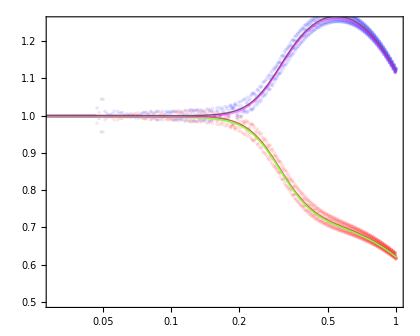

```mathematica
(* Comparison of the Potentials *)
ListLogLinearPlot[{DataΦ,DataΨ}//Abs,PlotRange->All,PlotStyle->{Directive[PointSize[0.006],Red,Opacity[0.1]],Directive[PointSize[0.006],Blue,Opacity[0.1]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},RotateLabel->False,BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{Full}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,30},LegendMarkerSize->{25,25}],
{0.32,0.38}],ImageSize->420,AspectRatio->0.8];
LogLinearPlot[{(ΦQSASHA2[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(ΦQSASHA2[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsQSASHA2,(Φstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Φstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsstd,(ΨQSASHA2[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(ΨQSASHA2[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsQSASHA2,(Ψstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Ψstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsstd}/.b->bHS/.k->300H0//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[RGBColor[0.8,0.4,0.3],Thick],Directive[Thick,RGBColor[0.5,1,0.2]],Directive[RGBColor[0.5,0.3,0.5],Thick],Directive[Thick,Magenta,Opacity[0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},RotateLabel->False,BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{std}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{std}"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,10},LegendMarkerSize->{35,15}],
{0.3,0.18}],ImageSize->420,AspectRatio->0.8];
Show[%%,%,PlotRange->{{Log[0.03],Log[1]},{0.5,1.25}},Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.2,0.82}]]}]
```

```mathematica
(* Average to get more illustrative data *)
FilterΦ=MeanFilter[DataΦ[[All,2]],1];
Length/@{FilterΦ,DataΦ}
FilterΨ=MeanFilter[DataΨ[[All,2]],1];
Length/@{FilterΨ,DataΨ}
```

{1000,1000}

{1000,1000}

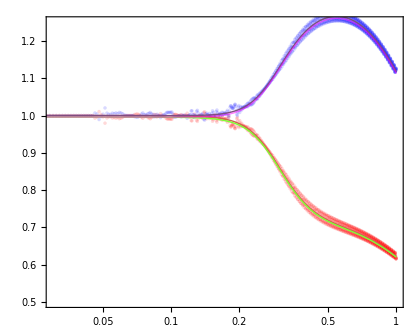

```mathematica
(* Comparison of the Potentials *)
ListLogLinearPlot[{Table[{DataΦ[[i,1]],FilterΦ[[i]]},{i,1,Length[FilterΦ]}],Table[{DataΨ[[i,1]],FilterΨ[[i]]},{i,1,Length[FilterΨ]}]}//Abs,PlotRange->All,PlotStyle->{Directive[PointSize[0.006],Red,Opacity[0.15]],Directive[PointSize[0.006],Blue,Opacity[0.15]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},RotateLabel->False,BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{Full}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,30},LegendMarkerSize->{25,25}],
{0.32,0.38}],ImageSize->420,AspectRatio->0.8];
LogLinearPlot[{(ΦQSASHA2[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(ΦQSASHA2[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsQSASHA2,(Φstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Φstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsstd,(ΨQSASHA2[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(ΨQSASHA2[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsQSASHA2,(Ψstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Ψstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsstd}/.b->bHS/.k->300H0//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[RGBColor[0.8,0.4,0.3],Thick],Directive[Thick,RGBColor[0.5,1,0.2]],Directive[RGBColor[0.5,0.3,0.5],Thick],Directive[Thick,Magenta,Opacity[0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},RotateLabel->False,BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{std}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{std}"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,10},LegendMarkerSize->{35,15}],
{0.3,0.18}],ImageSize->420,AspectRatio->0.8];
Show[%%,%,PlotRange->{{Log[0.03],Log[1]},{0.5,1.25}},Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.2,0.82}]]}]
```

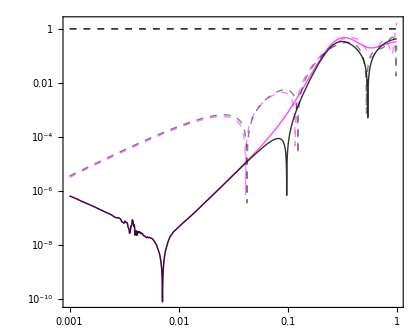

```mathematica
(* Comparison of the several ε parameters  *)
LogLogPlot[{D[ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.SolPertsQSASHA2,ΦSR'[a]/(ΦSR[a]*a*HN[Log[a]]^2),D[ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.SolPertsQSASHA2,ΨSR'[a]/(ΨSR[a]*a*HN[Log[a]]^2),1}/.b->bHS/.k->300//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[Thick,Magenta,Opacity[0.7]],Directive[Thick,Dashed,Magenta,Opacity[0.5]],Directive[Thick,Black,Opacity[0.8]],Directive[Thick,Black,Opacity[0.5],Dashed],Directive[Thick,Black,Dashed]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Phi^\\text{SHA, 2}"],(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Phi^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Psi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Psi^\\text{Full}"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.72,0.19}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.2,0.8}]]}]
```

```mathematica
(* Values of Subscript[ε, Φ] and Subscript[ε, Ψ] today *)
D[ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.k->300H0/.b->bHS/.SolPertsQSASHA2/.a->1
D[ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.k->300H0/.b->bHS/.SolPertsQSASHA2/.a->1
```

-0.433275

-0.334852

### Density Contrast

```mathematica
(* Full expression for the DE contrast using the analytical expressions *)
δFull=1/ρDEHS[a](((2 k^2)/((a^)^2)-(F k^2)/((a^)^2)-3 F (H^)^2-3 F Ḣ+72 Subscript[F, R] (H^)^2 Ḣ+18 Subscript[F, R] H^ H^(..)) (^(1)Φ^)+(6 H^-3 F H^-72 Subscript[F, R] H^ Ḣ-18 Subscript[F, R] H^(..)) (^(1)Φ̇)+((F k^2)/((a^)^2)-6 (H^)^2+3 F (H^)^2-3 F Ḣ+216 Subscript[F, R] (H^)^2 Ḣ+54 Subscript[F, R] H^ H^(..)) (^(1)Ψ^)+3 F H^ (^(1)Ψ̇))/.ah[]->a/.H^(..)->HN[Ne]*(HN'[Ne]^2+HN[Ne]*HN''[Ne])/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
δ1[A_]:=δFull/.(^(1)Φ^)->3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.SolPertsstd/.b->bHS/.k->300H0/.a->A
δ2[A_]:=δFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.SolPertsQSASHA2/.b->bHS/.k->300H0/.a->A
```

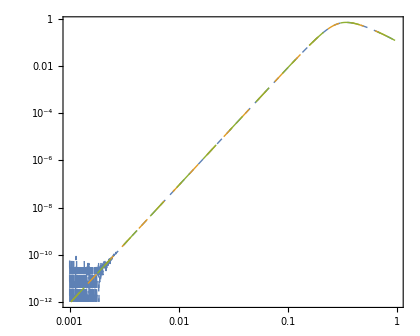

```mathematica
LogLogPlot[{δ2[a],δρQSASHA2[Log[a]]*(3 H0^2 Ωm[Log[a]])/ρDEHS[a] δm[a]/.SolPertsQSASHA2,δρDEstd[Log[a]]*(3 H0^2 Ωm[Log[a]])/ρDEHS[a]*δm[a]/.SolPertsstd}/.k->300H0/.b->bHS//Abs//Evaluate,{a,ai,1},PlotRange->{3,10^-12},PlotStyle->{Directive[Dashed,Thick],Directive[Dashing[Medium],Thick],Directive[Dashing[Large],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}^\\text{SHA,2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}^\\text{std}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.18,0.76}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.78,0.25}]]}]//Quiet
```

### Scalar Velocity

```mathematica
(* Full expression for the DE velocity using the analytical expressions *)
VFull=1/ρDEHS[a](((F k^2 H^)/a^-(24 Subscript[F, R] k^2 H^ Ḣ)/a^-(6 Subscript[F, R] k^2 H^(..))/a^) (^(1)Φ^)+(-(2 k^2)/a^+(F k^2)/a^) (^(1)Φ̇)+((2 k^2 H^)/a^-(F k^2 H^)/a^-(48 Subscript[F, R] k^2 H^ Ḣ)/a^-(12 Subscript[F, R] k^2 H^(..))/a^) (^(1)Ψ^)-(F k^2 (^(1)Ψ̇))/a^)/.ah[]->a/.H^(..)->HN[Ne]*(HN'[Ne]^2+HN[Ne]*HN''[Ne])/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
V1[A_]:=VFull/.(^(1)Φ^)->3Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.SolPertsstd/.b->bHS/.k->300H0/.a->A
V2[A_]:=VFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.SolPertsQSASHA2/.b->bHS/.k->300H0/.a->A
```

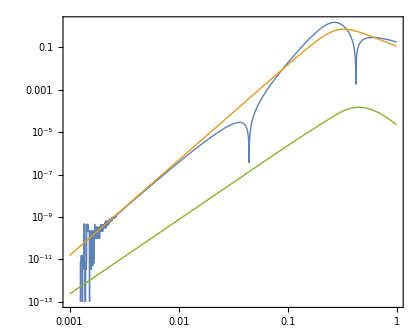

```mathematica
LogLogPlot[{V1[a],VQSASHA2[Log[a]]*(3 H0^2 Ωm[Log[a]])/ρDEHS[a] δm[a]/.SolPertsQSASHA2,VDEstd[Log[a]]*(3 H0^2 Ωm[Log[a]])/ρDEHS[a] δm[a]/.SolPertsstd}/.k->300H0/.b->bHS//Abs//Evaluate,{a,ai,1},PlotRange->{10,10^-13},PlotStyle->{Directive[Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}^\\text{SHA,2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}^\\text{std}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.18,0.76}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.78,0.18}]]}]//Quiet
```

### Sound Speed

```mathematica
(* Full expression for the DE Pressure perturbation -> Use it to compute Subscript[c, s]^2 *)
δPFull=(-6 H^+4 F H^) (^(1)Φ̇)+(-2+F) (^(1)Φ^(..))-F (^(1)Ψ^(..))+(^(1)Ψ̇) (2 H^-4 F H^-3 F')+(^(1)Ψ^) (-(2 k^2)/(3 (a^)^2)+6 (H^)^2-3 F (H^)^2+4 Ḣ-3 F Ḣ-6 H^ F'-3 F'')+(^(1)Φ^) (-(2 k^2)/(3 (a^)^2)+3 F (H^)^2+F Ḣ-2 H^ F'-F'')/.ah[]->a/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.f->f[R]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
δP1[A_]:=δPFull/.(^(1)Φ^)->3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.SolPertsstd/.b->bHS/.k->300H0/.a->A
δP2[A_]:=δPFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.SolPertsQSASHA2/.b->bHS/.k->300H0/.a->A
```

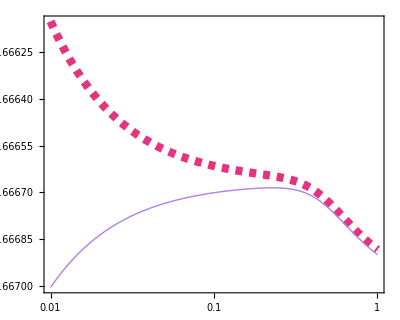

```mathematica
LogLinearPlot[{δP2[a]/(ρDEHS[a]*δ2[a]),cs2QSASHA2[Log[a]],δPDEstd[Log[a]]/δρDEstd[Log[a]]}/.k->300H0/.b->bHS//Evaluate,{a,0.01,1},PlotRange->All,PlotStyle->{Directive[Black,Opacity[0.8],Thick],Directive[Thickness[0.015],Dashed,RGBColor[0.9,0.2,0.5]],Directive[Thick,RGBColor[0.7,0.5,0.9]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["c_{s, \\text{Full}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{s, \\text{SHA}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{s, \\text{std}}^2"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.82,0.75}],ImageSize->400,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.45,0.78}]]}]//Quiet
```

### Effective Sound Speed

```mathematica
πFull=k^2/a^2*(FR*δR-(1-F)((^(1)Φ^)+(^(1)Ψ^)))/.δR->(4 k^2 (^(1)Φ^))/((a^)^2)+24 H^ (^(1)Φ̇)+6 (^(1)Φ^(..))+(2 k^2 (^(1)Ψ^))/((a^)^2)-24 (H^)^2 (^(1)Ψ^)-12 Ḣ (^(1)Ψ^)-6 H^ (^(1)Ψ̇)/.ah[]->a/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.f->f[R]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
π1[A_]:=πFull/.(^(1)Φ^)->3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.SolPertsstd/.b->bHS/.k->300H0/.a->A
π2[A_]:=πFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.SolPertsQSASHA2/.b->bHS/.k->300H0/.a->A
```

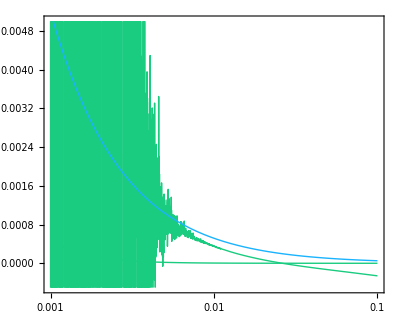

```mathematica
LogLinearPlot[{δP2[a]/(ρDEHS[a]*δ2[a])-2/3*π2[a]/(ρDEHS[a]*δ2[a]),cs2effQSASHA2[Log[a]],δPDEstd[Log[a]]/δρDEstd[Log[a]]-2/3*πDEstd[Log[a]]/δρDEstd[Log[a]]}/.k->300H0/.b->bHS//Evaluate,{a,ai,0.1},PlotRange->{-0.0005,0.005},PlotStyle->{Directive[Thick,RGBColor[0.1,0.8,0.5]],Directive[Thick,RGBColor[0.1,0.7,1]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(*(MaTeX[#,Magnification->1.3]&)/@Style["c_{\\text{eff}, \\text{Full}}^2"],*)
(MaTeX[#,Magnification->1.3]&)/@Style["c_{\\text{eff}, \\text{SHA}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{\\text{eff}, \\text{std}}^2"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.81,0.75}],ImageSize->400,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.81,0.35}]]}]//Quiet
```

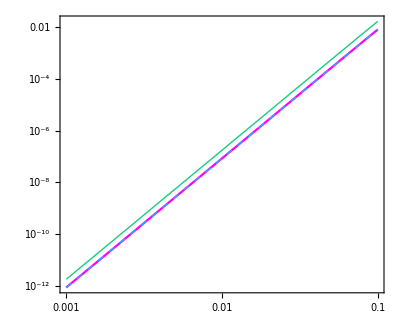

```mathematica
(* There are no changes in Subscript[π, DE] -> Expected since Subscript[π, DE] ∝ Subscript[δ, DE] *)
LogLogPlot[{π2[a],πQSASHA2[Log[a]](3 H0^2 Ωm[Log[a]])/ρDEHS[a]*δm[a]/.SolPertsQSASHA2,πDEstd[Log[a]](3 H0^2 Ωm[Log[a]])/ρDEHS[a]*δm[a]/.SolPertsstd}/.k->300H0/.b->bHS//Evaluate,{a,ai,0.1},PlotRange->All,PlotStyle->{Directive[Thick,RGBColor[0.1,0.8,0.5]],Directive[Magenta],Directive[Thick,RGBColor[0.1,0.7,1],Dashed]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\pi_\\text{DE}^{\\text{Full}}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\pi_\\text{DE}^{\\text{SHA}}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\pi_\\text{DE}^{\\text{std}}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.18,0.75}],ImageSize->400,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.81,0.35}]]}]//Quiet
```

### Viscosity Parameter

```mathematica
(* Indeed, we define: Subscript[c, a]^2(1 + w) *)
c2a[a_]:=wHSapprox[a](1+wHSapprox[a])-D[wHSapprox[b],b]/(a*HN[Log[a]])/.b->a
```

```mathematica
c2visFull[a_]:=(a*HN[Log[a]](1+wHSapprox[a]))/(4wHSapprox[a]*V2[a])(3c2a[a]*π2[a]+wHSapprox[a](a D[π2[d],d]-3wHSapprox[a]*π2[a]))/.d->a
c2visstd[a_]:=(a*HN[Log[a]](1+wHSapprox[a]))/(4wHSapprox[a]*VDEstd[Log[a]]*(3 H0^2 Ωm[Log[a]])/ρDEHS[a] δm[a])(3c2a[a]*πDEstd[Log[a]]*(3 H0^2 Ωm[Log[a]])/ρDEHS[a] δm[a]+wHSapprox[a](a D[πDEstd[Log[d]]*(3 H0^2 Ωm[Log[d]])/ρDEHS[d] δm[d],d]-3wHSapprox[a]*πDEstd[Log[a]]*(3 H0^2 Ωm[Log[a]])/ρDEHS[a] δm[a]))/.d->a
c2visQSA[a_]:=(a*HN[Log[a]](1+wHSapprox[a]))/(4wHSapprox[a]*VQSASHA2[Log[a]]*(3 H0^2 Ωm[Log[a]])/ρDEHS[a] δm[a])(3c2a[a]*πQSASHA2[Log[a]]*(3 H0^2 Ωm[Log[a]])/ρDEHS[a] δm[a]+wHSapprox[a](a D[πQSASHA2[Log[d]]*(3 H0^2 Ωm[Log[d]])/ρDEHS[d] δm[d],d]-3wHSapprox[a]*πQSASHA2[Log[a]]*(3 H0^2 Ωm[Log[a]])/ρDEHS[a] δm[a]))/.d->a
```

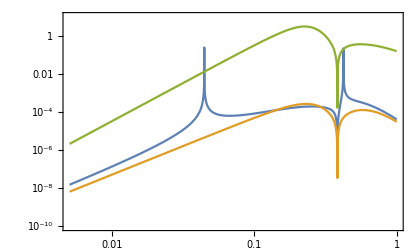

```mathematica
c2visFull[a];
c2visQSA[a];
c2visstd[a];
LogLogPlot[{%%%,%%/.SolPertsQSASHA2,%/.SolPertsstd}/.b->bHS/.k->300H0//Abs//Evaluate,{a,0.005,1},PlotRange->{All,{10^-10,10}},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["c^2_\\text{vis, Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["c^2_\\text{vis, SHA}"],
(MaTeX[#,Magnification->1.3]&)/@Style["c^2_\\text{vis, std}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.56,0.12}],ImageSize->420,AspectRatio->0.6,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.2,0.82}]]}]//Quiet
```

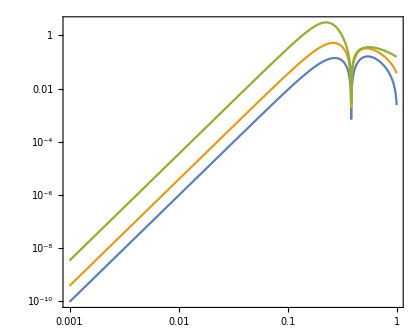

```mathematica
(* This is Fig. 9 in 1811.02469 *)
c2visstd[a];
LogLogPlot[%/.SolPertsstd/.b->bHS/.k->{50,100,300}H0//Abs//Evaluate,{a,ai,1},PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a","c^2_\\text{vis}"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["k = 50 H_0"],
(MaTeX[#,Magnification->1.3]&)/@Style["k = 100 H_0"],
(MaTeX[#,Magnification->1.3]&)/@Style["k = 300 H_0"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.78,0.25}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.2]&)/@Style["- \\quad \\text{Standard QSA-SHA}"],Scaled[{0.28,0.85}]]}]//Quiet
```

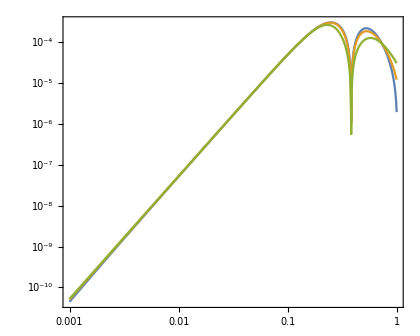

```mathematica
c2visQSA[a];
LogLogPlot[%/.SolPertsQSASHA2/.b->bHS/.k->{50,100,300}H0//Abs//Evaluate,{a,ai,1},PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a","c^2_\\text{vis}"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["k = 50 H_0"],
(MaTeX[#,Magnification->1.3]&)/@Style["k = 100 H_0"],
(MaTeX[#,Magnification->1.3]&)/@Style["k = 300 H_0"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.78,0.25}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.2]&)/@Style["- \\quad \\text{New QSA-SHA}"],Scaled[{0.28,0.85}]]}]//Quiet
```

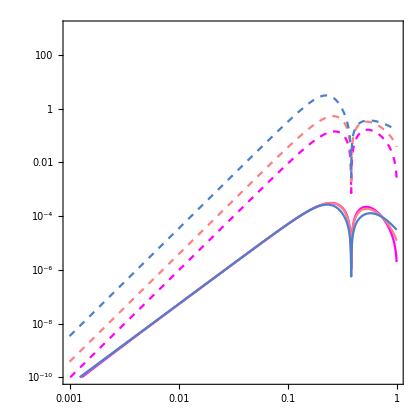

```mathematica
c2visstd[a];
c2visQSA[a];
LogLogPlot[{%/.SolPertsQSASHA2,%%/.SolPertsstd}/.b->bHS/.k->{50,100,300}H0//Abs//Evaluate,{a,ai,1},PlotRange->{10^-10,1000},PlotStyle->{Directive[Magenta],Directive[Pink],Directive[RGBColor[0.3,0.5,0.8]],Directive[Magenta,Dashed],Directive[Pink,Dashed],Directive[RGBColor[0.3,0.5,0.8],Dashed]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["k = 50 H_0"],
(MaTeX[#,Magnification->1.3]&)/@Style["k = 100 H_0"],
(MaTeX[#,Magnification->1.3]&)/@Style["k = 300 H_0"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.2,0.82}],ImageSize->420,AspectRatio->1,Epilog->{Text[(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Standard QSA-SHA}"],Scaled[{0.7,0.88}]],Text[(MaTeX[#,Magnification->1.2]&)/@Style["\\text{New QSA-SHA}"],Scaled[{0.75,0.2}]]}]//Quiet
```

```mathematica
{Ωm0,H0,ΩΛ}=.;
```

```mathematica
(* This is similar to Eq. (82) in 1811.02469 *)
Series[c2visstd[a]/.δm[a]->a/.Subscript[δ, m]'[a]->1,{a,0,4}]
```

-(16 (b k^2 (-1+Ωm0)) a^4)/(3 (H0^2 Ωm0^2))+O[a]^(9/2)

```mathematica
Series[c2visQSA[a]/.δm[a]->a/.δm'[a]->1,{a,0,6}]
```

-(16. (b k^2 (-1.+Ωm0)) a^4)/(H0^2 Ωm0^2)+(10.6667 b k^4 (-1.+Ωm0) a^5)/(H0^4 Ωm0^3)-(7.11111 (b (-1.+Ωm0) (1. k^6+25.3125 H0^6 Ωm0^2 ΩΛ)) a^6)/(H0^6 Ωm0^4)+O[a]^(13/2)

## Full Solution: k=100 H_0

### QSA-SHA Solutions

#### Standard Procedure

```mathematica
Φstd[Ne_]:=(2 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
Ψstd[Ne_]:=-(4 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δρDEstd[Ne_]:=-((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)/(F (3 Subscript[F, R] k^2+F (a^)^2))/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δPDEstd[Ne_]:=(2 Subscript[F, R] k^4+15 Subscript[F, R] k^2 (a^)^2 F''+3 F (a^)^4 F'')/(9 F Subscript[F, R] k^4+3 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]/.R->Ra[Ne]
VDEstd[Ne_]:=(a^ (6 Subscript[F, R] k^2+F (a^)^2) F')/(2 F (3 Subscript[F, R] k^2+F (a^)^2))/.ah[]->aN[Ne]/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]
πDEstd[Ne_]:=1/F*(k^2/a^2*FR/F)/(1+3 k^2/a^2*FR/F)/.a->aN[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);
Φistd=Φstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.b->bHS/.k->100H0/.a->ai//Quiet;
Ψistd=Ψstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.b->bHS/.k->100H0/.a->ai//Quiet;

(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[Φstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a];
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])Ψstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsstd=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.b->bHS/.k->100H0,{δm,Vm},{a,ai,1},MaxStepSize->10^-4,MaxStepFraction->10^-4,StartingStepSize->10^-4,PrecisionGoal->11,AccuracyGoal->11,MaxSteps->20000000,InterpolationOrder->All,Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### 2^nd Order in SHA

```mathematica
(* Don't forget the factors Subscript[ρ̄, m] Subscript[δ, m] for the potentials and Subscript[ρ̄, m]/Subscript[ρ̄, DE] Subscript[δ, m] for the other perturbations *)
ΦQSASHA2[Ne_]:=(2 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)-(3 ((a^)^2 (F^2 (a^)^4+F Subscript[F, R] k^2 (a^)^2 (8+δ)+2 Subscript[F, R]^2 k^4 (8+3 δ))) ε^2)/(2 (F (3 Subscript[F, R] k^3+F k (a^)^2)^2))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
ΨQSASHA2[Ne_]:=-(4 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)+(3 (a^)^2 (4 Subscript[F, R] k^2+F (a^)^2) (F (a^)^2+Subscript[F, R] k^2 (2-3 δ)) ε^2)/(2 F (3 Subscript[F, R] k^3+F k (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δρQSASHA2[Ne_]:=((2-3 F) Subscript[F, R] k^2-(-1+F) F (a^)^2)/(F (3 Subscript[F, R] k^2+F (a^)^2))-(3 (Subscript[F, R] k^2 (F (a^)^2 (1+δ)+2 Subscript[F, R] k^2 (2+3 δ))) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δPQSASHA2[Ne_]:=(2 Subscript[F, R] k^2)/(9 F Subscript[F, R] k^2+3 F^2 (a^)^2)+(((-1+F) F^2 (a^)^4 (1+2 δ)+F Subscript[F, R] k^2 (a^)^2 (-5+5 F-10 δ+13 F δ)+Subscript[F, R]^2 k^4 (-4-6 δ+3 F (2+7 δ))) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
VQSASHA2[Ne_]:=(((-4+3 F) Subscript[F, R] k^3+(-1+F) F k (a^)^2) ε)/(F (3 Subscript[F, R] k^2+F (a^)^2))/.ε->εSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
πQSASHA2[Ne_]:=(Subscript[F, R] k^2)/(3 F Subscript[F, R] k^2+F^2 (a^)^2)+(3 Subscript[F, R] k^2 (Subscript[F, R] k^2 (4+9 δ)+(F+2 F δ) (a^)^2) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
cs2QSASHA2[Ne_]:=-(2 (Subscript[F, R] k^2))/(3 (-2+3 F) Subscript[F, R] k^2+3 (-1+F) F (a^)^2)-(F ((-1+F)^2 F (a^)^4 (1+2 δ)+Subscript[F, R]^2 k^4 (-8+6 F-20 δ+21 F δ)+(-1+F) Subscript[F, R] k^2 (a^)^2 (-4-8 δ+F (5+13 δ))) ε^2)/(((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.α->αDES
cs2effQSASHA2[Ne_]:=((-((-1+F) F (a^)^2 (1+2 δ))+Subscript[F, R] k^2 (4+8 δ-F (2+7 δ))) ε^2)/((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.α->αDES
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);
ΦiQSASHA=ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.b->bHS/.k->100H0/.a->ai//Quiet;
ΨiQSASHA=ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.b->bHS/.k->100H0/.a->ai//Quiet;
(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a];
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsQSASHA2=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.b->bHS/.k->100H0,{δm,Vm},{a,ai,1},Method->{"EquationSimplification"->"Residual"}][[1]];
```

### Fortran Data

```mathematica
DataFortran=Import["/Users/cosmologygroup/Desktop/QSA_Project/Theoretical_Work/Bayron/HS_k_100.txt","Data"];
DataΔ=DataFortran[[All,{1,2}]];
Datav=DataFortran[[All,{1,3}]];
DataΦPlus=DataFortran[[All,{1,4}]];
Dataχ=DataFortran[[All,{1,5}]];
```

```mathematica
DataΦ=Table[{DataΦPlus[[i,1]],(-DataΦPlus[[i,2]]-Dataχ[[i,2]]/(2F))}/.F->f'[R]/.R->Ra[Ne]/.Ne->Log[DataΦPlus[[i,1]]]/.b->bHS//N,{i,1,Length[DataΦPlus]}];
DataΨ=Table[{DataΦPlus[[i,1]],(DataΦPlus[[i,2]]-Dataχ[[i,2]]/(2F))}/.F->f'[R]/.R->Ra[Ne]/.Ne->Log[DataΦPlus[[i,1]]]/.b->bHS//N,{i,1,Length[DataΦPlus]}];
```

### Potentials

```mathematica
ΦSR[a_]=ΦiQSASHA*FindFormula[DataΦ][a]//Expand
ΨSR[a_]=-ΨiQSASHA*FindFormula[DataΨ][a]//Expand
```

0.0000463271-0.00001592 a+0.000228688 a^2-0.0011717 a^3+0.00223208 a^4-0.00186335 a^5+0.000576476 a^6

-0.0000458103-0.0000171512 a+0.000240837 a^2.-0.0011717 a^3.+0.00226033 a^4.-0.00189117 a^5.+0.000582341 a^6.

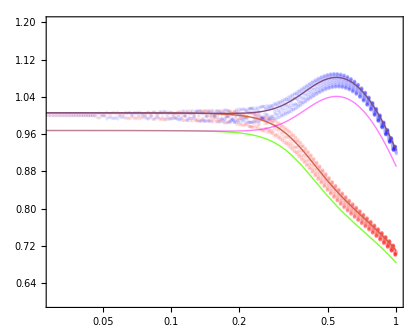

```mathematica
(* Comparison of the Potentials *)
ListLogLinearPlot[{DataΦ,DataΨ}//Abs,PlotRange->All,PlotStyle->{Directive[PointSize[0.006],Red,Opacity[0.1]],Directive[PointSize[0.006],Blue,Opacity[0.1]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},RotateLabel->False,BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{Full}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,30},LegendMarkerSize->{25,25}],
{0.32,0.38}],ImageSize->420,AspectRatio->0.8];
LogLinearPlot[{(ΦQSASHA2[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(ΦQSASHA2[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsQSASHA2,(Φstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Φstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsstd,(ΨQSASHA2[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(ΨQSASHA2[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsQSASHA2,(Ψstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Ψstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsstd}/.b->bHS/.k->100H0//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[RGBColor[0.8,0.4,0.3],Thick],Directive[Thick,RGBColor[0.5,1,0.2]],Directive[RGBColor[0.5,0.3,0.5],Thick],Directive[Thick,Magenta,Opacity[0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},RotateLabel->False,BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{std}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{std}"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,10},LegendMarkerSize->{35,15}],
{0.3,0.18}],ImageSize->420,AspectRatio->0.8];
Show[%%,%,PlotRange->{{Log[0.03],Log[1]},{0.6,1.2}},Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.2,0.82}]],Text[(MaTeX[#,Magnification->1.4]&)/@Style["k = 100 H_0"],Scaled[{0.8,0.12}]]}]
```

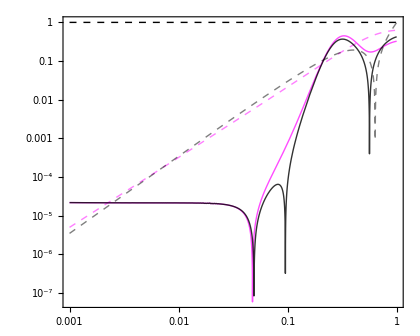

```mathematica
(* Comparison of the several ε parameters  *)
LogLogPlot[{D[ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.SolPertsQSASHA2,ΦSR'[a]/(ΦSR[a]*a*HN[Log[a]]^2),D[ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.SolPertsQSASHA2,ΨSR'[a]/(ΨSR[a]*a*HN[Log[a]]^2),1}/.b->bHS/.k->300//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[Thick,Magenta,Opacity[0.7]],Directive[Thick,Dashed,Magenta,Opacity[0.5]],Directive[Thick,Black,Opacity[0.8]],Directive[Thick,Black,Opacity[0.5],Dashed],Directive[Thick,Black,Dashed]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Phi^\\text{SHA, 2}"],(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Phi^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Psi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Psi^\\text{Full}"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.72,0.19}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.2,0.8}]]}]
```

```mathematica
(* Values of Subscript[ε, Φ] and Subscript[ε, Ψ] today *)
D[ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.k->500H0/.b->bHS/.SolPertsQSASHA2/.a->1
D[ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.k->500H0/.b->bHS/.SolPertsQSASHA2/.a->1
```

-0.45608

-0.412148

### Density Contrast

```mathematica
(* Full expression for the DE contrast using the analytical expressions *)
δFull=1/ρDEHS[a](((2 k^2)/((a^)^2)-(F k^2)/((a^)^2)-3 F (H^)^2-3 F Ḣ+72 Subscript[F, R] (H^)^2 Ḣ+18 Subscript[F, R] H^ H^(..)) (^(1)Φ^)+(6 H^-3 F H^-72 Subscript[F, R] H^ Ḣ-18 Subscript[F, R] H^(..)) (^(1)Φ̇)+((F k^2)/((a^)^2)-6 (H^)^2+3 F (H^)^2-3 F Ḣ+216 Subscript[F, R] (H^)^2 Ḣ+54 Subscript[F, R] H^ H^(..)) (^(1)Ψ^)+3 F H^ (^(1)Ψ̇))/.ah[]->a/.H^(..)->HN[Ne]*(HN'[Ne]^2+HN[Ne]*HN''[Ne])/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
δ1[A_]:=δFull/.(^(1)Φ^)->3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.SolPertsstd/.b->bHS/.k->100H0/.a->A
δ2[A_]:=δFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.SolPertsQSASHA2/.b->bHS/.k->100H0/.a->A
```

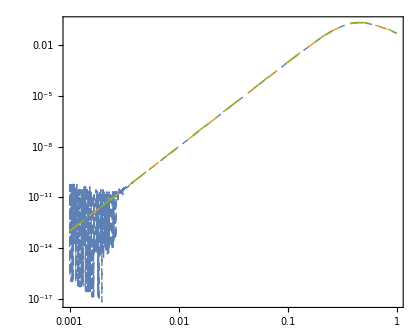

```mathematica
LogLogPlot[{δ2[a],δρQSASHA2[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a]/.SolPertsQSASHA2,δρDEstd[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a]/.SolPertsstd}/.k->100H0/.b->bHS//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[Dashed,Thick],Directive[Dashing[Medium],Thick],Directive[Dashing[Large],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}^\\text{SHA,2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}^\\text{std}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.18,0.76}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.78,0.25}]]}]//Quiet
```

### Scalar Velocity

```mathematica
(* Full expression for the DE velocity using the analytical expressions *)
VFull=1/ρDEHS[a](((F k^2 H^)/a^-(24 Subscript[F, R] k^2 H^ Ḣ)/a^-(6 Subscript[F, R] k^2 H^(..))/a^) (^(1)Φ^)+(-(2 k^2)/a^+(F k^2)/a^) (^(1)Φ̇)+((2 k^2 H^)/a^-(F k^2 H^)/a^-(48 Subscript[F, R] k^2 H^ Ḣ)/a^-(12 Subscript[F, R] k^2 H^(..))/a^) (^(1)Ψ^)-(F k^2 (^(1)Ψ̇))/a^)/.ah[]->a/.H^(..)->HN[Ne]*(HN'[Ne]^2+HN[Ne]*HN''[Ne])/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
V1[A_]:=VFull/.(^(1)Φ^)->3Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.SolPertsstd/.b->bHS/.k->100H0/.a->A
V2[A_]:=VFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.SolPertsQSASHA2/.b->bHS/.k->100H0/.a->A
```

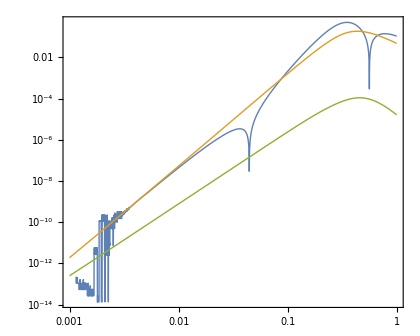

```mathematica
LogLogPlot[{V1[a],VQSASHA2[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a]/.SolPertsQSASHA2,VDEstd[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a]/.SolPertsstd}/.k->100H0/.b->bHS//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}^\\text{SHA,2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}^\\text{std}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.18,0.76}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.78,0.18}]]}]//Quiet
```

### Sound Speed

```mathematica
(* Full expression for the DE Pressure perturbation -> Use it to compute Subscript[c, s]^2 *)
δPFull=(-6 H^+4 F H^) (^(1)Φ̇)+(-2+F) (^(1)Φ^(..))-F (^(1)Ψ^(..))+(^(1)Ψ̇) (2 H^-4 F H^-3 F')+(^(1)Ψ^) (-(2 k^2)/(3 (a^)^2)+6 (H^)^2-3 F (H^)^2+4 Ḣ-3 F Ḣ-6 H^ F'-3 F'')+(^(1)Φ^) (-(2 k^2)/(3 (a^)^2)+3 F (H^)^2+F Ḣ-2 H^ F'-F'')/.ah[]->a/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.f->f[R]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
δP1[A_]:=δPFull/.(^(1)Φ^)->3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.SolPertsstd/.b->bHS/.k->100H0/.a->A
δP2[A_]:=δPFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.SolPertsQSASHA2/.b->bHS/.k->100H0/.a->A
```

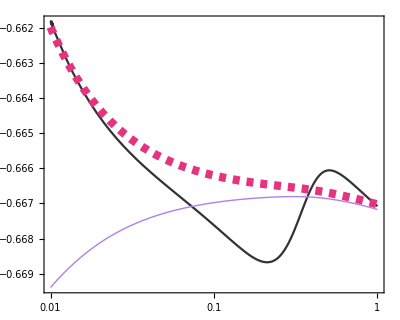

```mathematica
LogLinearPlot[{δP2[a]/(ρDEHS[a]*δ2[a]),cs2QSASHA2[Log[a]],δPDEstd[Log[a]]/δρDEstd[Log[a]]}/.k->100H0/.b->bHS//Evaluate,{a,0.01,1},PlotRange->All,PlotStyle->{Directive[Black,Opacity[0.8]],Directive[Thickness[0.015],Dashed,RGBColor[0.9,0.2,0.5]],Directive[Thick,RGBColor[0.7,0.5,0.9]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["c_{s, \\text{Full}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{s, \\text{SHA}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{s, \\text{std}}^2"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.82,0.25}],ImageSize->400,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.78,0.83}]]}]//Quiet
```

### Effective Sound Speed

```mathematica
πFull=k^2/a^2*(FR*δR-(1-F)((^(1)Φ^)+(^(1)Ψ^)))/.δR->(4 k^2 (^(1)Φ^))/((a^)^2)+24 H^ (^(1)Φ̇)+6 (^(1)Φ^(..))+(2 k^2 (^(1)Ψ^))/((a^)^2)-24 (H^)^2 (^(1)Ψ^)-12 Ḣ (^(1)Ψ^)-6 H^ (^(1)Ψ̇)/.ah[]->a/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.f->f[R]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
π1[A_]:=πFull/.(^(1)Φ^)->3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.SolPertsstd/.b->bHS/.k->100H0/.a->A
π2[A_]:=πFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.SolPertsQSASHA2/.b->bHS/.k->100H0/.a->A
```

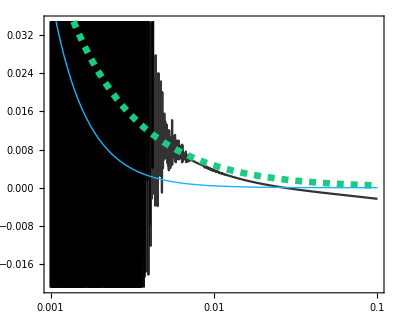

```mathematica
LogLinearPlot[{δP2[a]/(ρDEHS[a]*δ2[a])-2/3*π2[a]/(ρDEHS[a]*δ2[a]),cs2effQSASHA2[Log[a]],δPDEstd[Log[a]]/δρDEstd[Log[a]]-2/3*πDEstd[Log[a]]/δρDEstd[Log[a]]}/.k->100H0/.b->bHS//Evaluate,{a,ai,0.1},PlotRange->Automatic,PlotStyle->{Directive[Black,Opacity[0.8]],Directive[Thickness[0.012],Dashed,RGBColor[0.1,0.8,0.5]],Directive[Thick,RGBColor[0.1,0.7,1]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["c_{\\text{eff}, \\text{Full}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{\\text{eff}, \\text{SHA}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{\\text{eff}, \\text{std}}^2"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.81,0.75}],ImageSize->400,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(HS)}"],Scaled[{0.81,0.35}]]}]
```